# Discovering the Muon

In this project we consider a hypothetical 1 GeV e^+e^- collider as a tool to discover the muon. It should be noted that the muon was historically discovered in cosmic rays, not at a collider. However, for the sake of learning the very basics of how collider searches work we will pretend.

## Possibly Useful Functions

These are simply the functions that you likely made in the previous project. They are all given here in case you want to use them. They may or may not be necessary in what follows.

```mathematica
ClearMemory:=Module[{},
Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];
];(*This is just to try and ensure memory stays somewhat in control.*)
eventInfo={_,_,_,_,_,_};
decayedOrIn = {_,-1,_,_,_,_,_,_,_,_,_,_,_}  | {_,2,_,_,_,_,_,_,_,_,_,_,_};
SetOut[ event_ ]  := (DeleteCases[event,decayedOrIn,2]);
ReadLHE[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
(*Throw away header info at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{_String,___}| eventInfo,2]
);
ReadEvents[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadLHE[testp]; ]; 
(*convert raw data into readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info*)
ClearMemory;
{eventListp, eventListOutLp}
];
PIDu= 2;
PIDubar = -2;
PIDd = 1;
PIDdbar = -1;
PIDs = 3;
PIDsbar = -3;
PIDc = 4;
PIDcbar = -4;
PIDb = 5;
PIDbbar = -5;
PIDt = 6;
PIDtbar = -6;
PIDeminus = 11;
PIDeplus = -11;
PIDnue=12;
PIDnuebar = -12;
PIDmuminus = 13;
PIDmuplus =-13;
PIDnumu = 14;
PIDnumubar = -14;
PIDtauminus = 15;
PIDtauplus = -15;
PIDnutau = 16;
PIDnutaubar = -16;
PIDgluon = 21;
PIDphoton = 22;
PIDZ = 23;
PIDWplus = 24;
PIDWminus = -24;
PIDh = 25;

particle[2] ="u";
particle[-2] ="ū";

particle[1] ="d";
particle[-1] ="d̄";

particle[3] ="s";
particle[-3] ="s̄";

particle[4] ="c";
particle[-4] ="c̄";

particle[5] ="b";
particle[-5] ="b̄";

particle[6] ="t";
particle[-6] ="t̄";

particle[11] ="e^-";
particle[-11] ="e^+";

particle[12] ="ν_e";
particle[-12] ="ν_e^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="ν_μ";
particle[-14] ="ν_μ^c";


particle[15] ="τ^-";
particle[-15]="τ^+";

particle[16] ="ν_τ";
particle[-16] ="ν_τ^c";

particle[21] ="gluon";
particle[22] = "γ";
particle[23] = "Z";
particle[24] ="W^+";
particle[-24] = "W^-";
particle[25] = "h";

finout[-1] = "in";
finout[1] = "out";
finout[2]  = "decayed";

EventPrint[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,cτ,hel}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcCos[pz/(√(px^2 + py^2+ pz^2))];
phifn[px_,py_]:=Which[
 py > 0, 
ArcTan[px,py]
,
 py < 0, 
2π + ArcTan[px,py]

];(* This function is defined such that ϕ∈[0,2π]*)

phiOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= phifn[px,py];
theta[event_] := Map[thetaOf,event,{1}]//Flatten;
phi[event_] := Map[phiOf,event,{1}]//Flatten;
rapOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=1/2 Log[(e+pz)/(e-pz)];
etaOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=-Log[Tan[1/2 ArcCos[pz/(√(px^2 + py^2+ pz^2))]]];
rap[event_] := Map[rapOf,event,{1}]//Flatten;
eta[event_] := Map[etaOf,event,{1}]//Flatten;
ptOf[{_,_,_,_,_,_,px_,py_,___}]:=√(px^2+py^2);
enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=En;
pT[event_]  :=Map[ptOf,event,{1}]//Flatten;
en[event_]:=Map[enOf,event,{1}]//Flatten;
AbsMin[list_]:=Sort[list,Abs[#1]<Abs[#2]&]⟦1⟧;
DeltaPhi[{part1_,part2_}]:=AbsMin[{
(phiOf[part1]-phiOf[part2])
,
(2 π - (phiOf[part1]-phiOf[part2]))
,
(2 π + (phiOf[part1]-phiOf[part2]))
}];
DeltaR[{part1_,part2_}]:=√((etaOf[part1] - etaOf[part2])^2+DeltaPhi[{part1,part2}]^2);
FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}] := {En, px, py,pz };
FourLength[{En_,px_,py_,pz_}] := Sqrt[En^2 - px^2 - py^2-pz^2];
InvMass[particles_]:= FourLength[ Sum[FourVectorFrom[particles[[i]]],{i,1,Length[particles]}]];
```

## Searching for the Muon

In a real experiment that is producing electrically charged particles, say by colliding an electron and a positron, both electrons and muons (and other charged particles) will be produced if the center of mass energy is high enough. This will include things like the charged pions, but these are strongly interacting particles that we can use our hadronic calorimeter to exclude.

Suppose we are interested in discovering new leptons (particles like the electron). We assume the electron is a known particle, but that the muon is not.

In the experiment the production of the electrons we call the background, they are the electrically charged particles that we are not interested in. The production of muons we call the signal.

Recall that in project 1 the model we used set the masses of the electrons and the muons to be zero. As mass is the primary difference between these particles we need to include their masses. This can be done by using a different MadGraph model, called sm-full
This is used by opening MadGraph and then typing

import model sm-full

We also need to worry about what the actual experiment is sensitive to and looking for. Perhaps for this search it requires a Trigger. Only certain events pass the trigger and get recorded. Let’s suppose that they are worried that they cannot fully trust signal at the edge of their detectors. So, while the detector goes out to |η| < 2.5, they trigger only on charged particles with |η| < 2.4 . For our purposes we’ll require that both charged particles in an event satisfy this requirement.

Should we then change our simulation cuts in the run_card to match this trigger? 

Only partly, it is best to make the generator level cuts looser than the experimental ones so that edge effects do not affect your analysis. So, we keep the standard cut for simulation. 

We are also going to assume that the experiment cannot resolve the full 4-momentum of the charged particles. For this project that would make finding the muon too easy. Suppose that there is no electronic calorimeter to determine the energy of the particles. Without the energy the four-momentum cannot be reconstructed and hence the mass of the particles is unknown.

Instead, we assume they can infer the transverse momentum from the bending of the charged particle tracks in the magnetic field and also the electric charge. They also detect and record the values of ϕ and η  the particles have as they strike the detector components.

## Simulate the Background events

The background is e^+e^-→e^+e^- . 
Directive 1: Use MadGraph with the sm-full model to generate at least 10,000 background events. (10 pts)

Remember to change the run card so that the collider energy is 1 GeV and there is no cut on lepton p_T. Keep the standard  lepton rapidity cut. 

Look in the param_card to make sure you’ve loaded the correct model. You should find
###################################
## INFORMATION FOR MASS
###################################
Block mass 
    4 1.270000e+00 # MC 
    5 4.700000e+00 # MB 
    6 1.720000e+02 # MT 
   11 5.110000e-04 # Me 
   13 1.056600e-01 # MM 
   15 1.777000e+00 # MTA 
   23 9.118800e+01 # MZ 
   25 1.250000e+02 # MH 
Which shows that the electron (Me) and the muon (MM) have nonzero masses.

Question 1: What is the cross section in piccobarns? (2pts)
Answer: 3.915e7 +-  3.613e4 pb
This should be quite similar to the massless electron case (why?)
Because the electron’s mass is so small that it can be considered negligible.
Let’s record the amount in pb as a variable for use later

```mathematica
σbkgnd=3.915*10^7;
```

Let’s see how the events look
Directive 2: Read in the background events and make histograms of rapidity, η, p_T, and ΔR (8pts)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica\513\Project 2

```mathematica
(* Read in the event data *)
{ioeetoeeEvents,oeetoeeEvents}=ReadEvents["project2_backgroundevents.lhe"];
```

Time taken to read events: 3.04688

```mathematica
Length[ioeetoeeEvents]
Length[oeetoeeEvents]
ioeetoeeEvents[[11]]
oeetoeeEvents[[11]]
```

10000

10000

{{-11,-1,0,0,0,0,0.,0.,0.5,0.5,0.000511,0.,-1.},{11,-1,0,0,0,0,0.,0.,-0.5,0.5,0.000511,0.,1.},{-11,1,1,2,0,0,-0.106719,0.00812898,0.48841,0.5,0.000511,0.,-1.},{11,1,1,2,0,0,0.106719,-0.00812898,-0.48841,0.5,0.000511,0.,1.}}

{{-11,1,1,2,0,0,-0.106719,0.00812898,0.48841,0.5,0.000511,0.,-1.},{11,1,1,2,0,0,0.106719,-0.00812898,-0.48841,0.5,0.000511,0.,1.}}

```mathematica
(* Test our above function *)
EventPrint[ioeetoeeEvents[[11]]]
EventPrint[oeetoeeEvents[[11]]]
```

(# | pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | cτ | hel
1 | e^+ | in | 0 | 0 | 0 | 0 | 0. | 0. | 0.5 | 0.5 | 0.000511 | 0. | -1.
2 | e^- | in | 0 | 0 | 0 | 0 | 0. | 0. | -0.5 | 0.5 | 0.000511 | 0. | 1.
3 | e^+ | out | 1 | 2 | 0 | 0 | -0.106719 | 0.00812898 | 0.48841 | 0.5 | 0.000511 | 0. | -1.
4 | e^- | out | 1 | 2 | 0 | 0 | 0.106719 | -0.00812898 | -0.48841 | 0.5 | 0.000511 | 0. | 1.)

(# | pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | cτ | hel
1 | e^+ | out | 1 | 2 | 0 | 0 | -0.106719 | 0.00812898 | 0.48841 | 0.5 | 0.000511 | 0. | -1.
2 | e^- | out | 1 | 2 | 0 | 0 | 0.106719 | -0.00812898 | -0.48841 | 0.5 | 0.000511 | 0. | 1.)

```mathematica
(* Test our functions *)
thetaOf[ioeetoeeEvents[[11,1]]]
phiOf[ioeetoeeEvents[[11,1]]]
thetaOf[ioeetoeeEvents[[11,2]]]
phiOf[ioeetoeeEvents[[11,2]]]
```

0.

3.14159

```mathematica
(* Create our data*)
thetaList=Flatten[theta/@oeetoeeEvents];
phiList=Flatten[phi/@oeetoeeEvents];
```

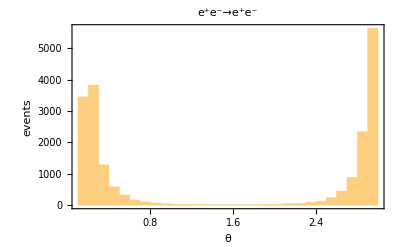

```mathematica
(* Histogram of theta *)
Histogram[thetaList,{0.1},PlotLabel->"e^+e^-→e^+e^-",Frame->True, FrameLabel->{"θ","events"},BaseStyle->{FontSize->14}]
```

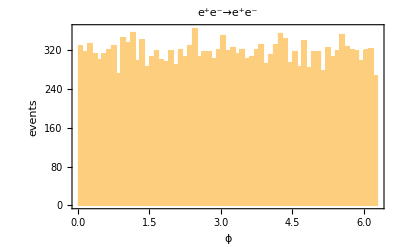

```mathematica
(* Histogram of phi *)
Histogram[phiList,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"ϕ","events"},BaseStyle->{FontSize->14}]
```

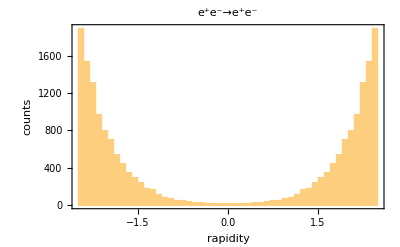

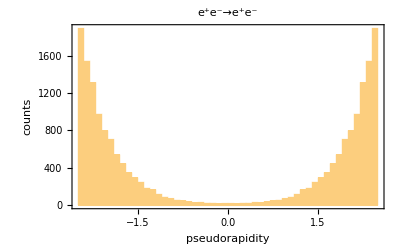

```mathematica
(* Histograms of rapidity and pseudorapidity *)
rapList=Flatten[rap/@oeetoeeEvents];
etaList=Flatten[eta/@oeetoeeEvents];
Histogram[rapList,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"rapidity","counts"},BaseStyle->{FontSize->14}]
Histogram[etaList,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"pseudorapidity","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
(* On to Subscript[p, T] and Energy *)
pTList=Flatten[pT/@oeetoeeEvents];
enList=Flatten[en/@oeetoeeEvents];
```

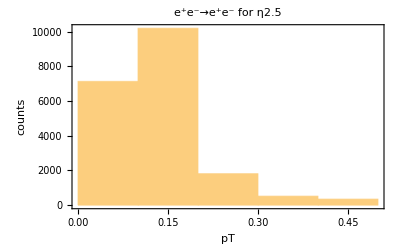

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTList,{0.1},PlotLabel->"e^+e^-→e^+e^- for η2.5", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
(* Energy Histogram *)
Histogram[enList,{0.1},PlotLabel->"e^+e^-→e^+e^- for η2.5", Frame->True, FrameLabel->{"E","counts"},BaseStyle->{FontSize->14}]
```

-Graphics-

```mathematica
(* Define a list for DeltaR *)
DeltaRList=Flatten[DeltaR/@oeetoeeEvents];
```

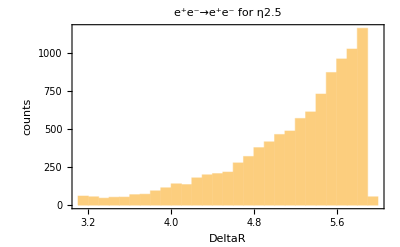

```mathematica
(* Histogram for Delta R*)
Histogram[DeltaRList,{0.1},PlotLabel->"e^+e^-→e^+e^- for η2.5", Frame->True, FrameLabel->{"DeltaR","counts"},BaseStyle->{FontSize->14}]
```

## Simulating the Signal

Directive 3: Simulate at least 10,000 signal events. (10 pts)
Use the same MadGraph model as you did for the signal, but now type 
e+ e- > mu+ mu-
that is, the production of muons at an e+ e- collider. 

Keep the energy of the collider at 1 GeV and the usual |η| < 2.5 cut. But remember to remove the cut on lepton p_T.

Question 2: What is the cross section? How does it compare to the production of electrons? (4pts)
Answer: 9.278e4 +- 109.6
It is about 3 orders of magnitude lower than that of the production of electrons.

Record the signal cross section for later use

```mathematica
σsignal=9.278*10^4;
```

Directive 4: Read in the signal events and make histograms of rapidity, η, p_T, and ΔR (8 pts)

Time taken to read events: 4.51563

10000

10000

{{-11,-1,0,0,0,0,0.,0.,0.5,0.5,0.000511,0.,1.},{11,-1,0,0,0,0,0.,0.,-0.5,0.5,0.000511,0.,-1.},{-13,1,1,2,0,0,-0.182337,0.335156,-0.305385,0.5,0.10566,0.,-1.},{13,1,1,2,0,0,0.182337,-0.335156,0.305385,0.5,0.10566,0.,1.}}

{{-13,1,1,2,0,0,-0.182337,0.335156,-0.305385,0.5,0.10566,0.,-1.},{13,1,1,2,0,0,0.182337,-0.335156,0.305385,0.5,0.10566,0.,1.}}

(# | pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | cτ | hel
1 | e^+ | in | 0 | 0 | 0 | 0 | 0. | 0. | 0.5 | 0.5 | 0.000511 | 0. | 1.
2 | e^- | in | 0 | 0 | 0 | 0 | 0. | 0. | -0.5 | 0.5 | 0.000511 | 0. | -1.
3 | μ^+ | out | 1 | 2 | 0 | 0 | -0.182337 | 0.335156 | -0.305385 | 0.5 | 0.10566 | 0. | -1.
4 | μ^- | out | 1 | 2 | 0 | 0 | 0.182337 | -0.335156 | 0.305385 | 0.5 | 0.10566 | 0. | 1.)

(# | pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | cτ | hel
1 | μ^+ | out | 1 | 2 | 0 | 0 | -0.182337 | 0.335156 | -0.305385 | 0.5 | 0.10566 | 0. | -1.
2 | μ^- | out | 1 | 2 | 0 | 0 | 0.182337 | -0.335156 | 0.305385 | 0.5 | 0.10566 | 0. | 1.)

0.

3.14159

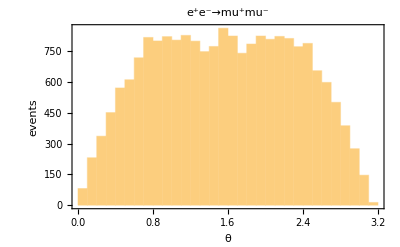

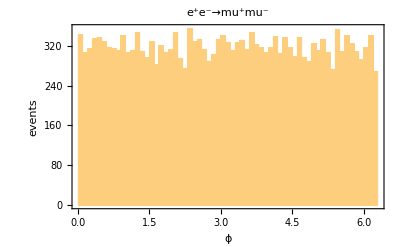

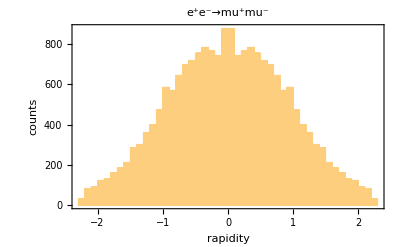

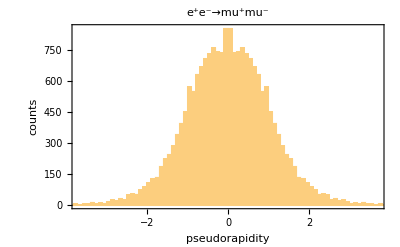

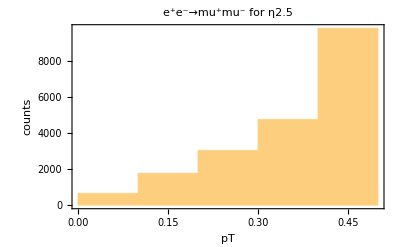

-Graphics-

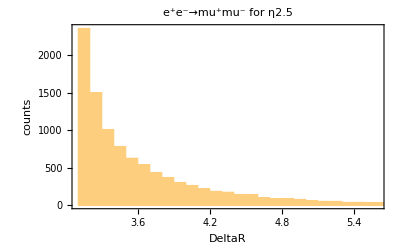

```mathematica
(* Read in the event data *)
{ioeetouuEvents,oeetouuEvents}=ReadEvents["project2_mu_mu_events.lhe"];
Length[ioeetouuEvents]
Length[oeetouuEvents]
ioeetouuEvents[[11]]
oeetouuEvents[[11]]
(* Test our above function *)
EventPrint[ioeetouuEvents[[11]]]
EventPrint[oeetouuEvents[[11]]]
(* Test our functions *)
thetaOf[ioeetouuEvents[[11,1]]]
phiOf[ioeetouuEvents[[11,1]]]
thetaOf[ioeetouuEvents[[11,2]]]
phiOf[ioeetouuEvents[[11,2]]]
(* Create our data*)
thetaListu=Flatten[theta/@oeetouuEvents];
phiListu=Flatten[phi/@oeetouuEvents];
(* Histogram of theta *)
Histogram[thetaListu,{0.1},PlotLabel->"e^+e^-→mu^+mu^-",Frame->True, FrameLabel->{"θ","events"},BaseStyle->{FontSize->14}]
(* Histogram of phi *)
Histogram[phiListu,{0.1},PlotLabel->"e^+e^-→mu^+mu^-", Frame->True, FrameLabel->{"ϕ","events"},BaseStyle->{FontSize->14}]
(* Histograms of rapidity and pseudorapidity *)
rapListu=Flatten[rap/@oeetouuEvents];
etaListu=Flatten[eta/@oeetouuEvents];
Histogram[rapListu,{0.1},PlotLabel->"e^+e^-→mu^+mu^-", Frame->True, FrameLabel->{"rapidity","counts"},BaseStyle->{FontSize->14}]
Histogram[etaListu,{0.1},PlotLabel->"e^+e^-→mu^+mu^-", Frame->True, FrameLabel->{"pseudorapidity","counts"},BaseStyle->{FontSize->14}]
(* On to Subscript[p, T] and Energy *)
pTListu=Flatten[pT/@oeetouuEvents];
enListu=Flatten[en/@oeetouuEvents];
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for η2.5", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
(* Energy Histogram *)
Histogram[enListu,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for η2.5", Frame->True, FrameLabel->{"E","counts"},BaseStyle->{FontSize->14}]
(* Define a list for DeltaR *)
DeltaRListu=Flatten[DeltaR/@oeetouuEvents];
(* Histogram for Delta R*)
Histogram[DeltaRListu,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for η2.5", Frame->True, FrameLabel->{"DeltaR","counts"},BaseStyle->{FontSize->14}]
```

Question 3: What distributions look similar to the background, what looks different? (4pts)
Answer: The theta graph is wildly different. It is opposite. The middle theta values are the highest, unlike for the background. DeltaR is flipped over the y-axis. The transverse momentum is also flipped over the y-axis and it is more consistent. The rapidity is also opposite, just like the theta graph. The muon rapidity looks like a bell curve, whereas the background looks like a parabola.

## Dealing with Uncertainty

We are thinking of using simulated events to make estimates of what will occur in experimental situations. To this end we want to characterize the error inherent in such simulations and how that will translate into the experiment. The experimental results have similar error analyses as they try to find the true probability distribution from a finite amount of data.

If we observe N events in a histogram bin, what is the error for the estimate of the actual average rate of that bin to confidence level CL ∈ (0,1)?
The confidence level is related to σs, for instance 2σ is about 95% confidence.

The code below considers a Poisson distribution with mean = number of events in the bin
Given that distribution, it then returns how many events would be expected away from the mean, to some level of confidence, on either side of the mean.

In the code below we focus on 1-σ error on either side, or  about 68% confidence.

```mathematica
PoissonError[nobs_,CL_]:={ If[nobs ==  0, 0, InverseCDF[PoissonDistribution[nobs],1-CL]],
If[nobs==0,0,InverseCDF[PoissonDistribution[nobs],CL]]}//N

(*Default is 1-σ error*)
PoissonError[nobs_]:=PoissonError[nobs, Erf[1/Sqrt[2]]]-nobs;
```

## Cutting the Data

Now, it is clear that there are many more muons that are produced at smaller η, or equivalently with larger p_T. Let’s design a cut strategy to maximize the muon signal over the electron background. Remember, the electron cross section is about 100 times larger, so we really need to find the place where the muons dominate.

Before we begin we also need to know a little more about our pretend collider. Suppose that over the course of the experimental run 1 inverse nanobarn, 1 nb^-1, of integrated luminosity was recorded. Then the total number of events is given by
num. events = cross section × Luminosity

But we recorded all our cross sections in piccobarns (pb) not nb. 
Question 4: What is the luminosity in inverse piccobarns? (2pts)
Answer: 10^3
Let’s record that below for future use.

```mathematica
Lumipb=10^-3;
```

We can now determine the number of background and signal events we expect to be recorded by the experiment
Question 5: Which is expected to produce more events, the signal or the background? By how much? (4pts)
Answer: The background is expected to produce more events by a factor of 1000

```mathematica
Nbkgnd=σbkgnd*Lumipb
Nsignal=σsignal*Lumipb
```

39150.

92.78

A somewhat useful characterization is the ratio
N_signal/N_background
Question 6: What is the signal over the background? (2 pts)
Answer: 0.00236986
The more useful way of evaluating significance is
N_signal/√N_background
Question 7: What is the signal over the square-root of the background? (2 pts)
Answer: .486909

```mathematica
Nsignal/Nbkgnd
Nsignal/√Nbkgnd
```

0.00236986

0.468909

In order to claim discovery, we need N_signal/√N_background≥ 5 .
We do this by making planning to only look at specific types of events where we expect much more signal than background. This is called making “cuts” of the data.

By looking at the histograms for the background and the signal, we see that if we require the transverse momentum of both particles in the event to be p_T≥ 0.2 then we keep most of the signal and but cut out a lot of the background. But will that be enough? Let’s try a few more stringent cuts to see what happens

In general we may have several cuts, so let’s make a process that can account for whatever we may need later.
First we define a list of our cuts,

```mathematica
cutnames ={
"No Cuts",(*1*)
"Trigger: |η|<2.4",(*2*)
" p_T≥0.2 GeV", (*3*)
" p_T≥0.25 GeV", (*4*)
" p_T≥0.3 GeV", (*5*)
" p_T≥0.35 GeV", (*6*)
" p_T≥0.4 GeV", (*7*)
" p_T≥0.45 GeV" (*8*)
};
```

Now, we create a function that implements the triggering and cuts. This function will record the number of events that pass the trigger or cut. 

The code below is not sophisticated. Make sure you understand what it is doing.

```mathematica
ApplyCuts[eventlist_]:=Module[{currentevent,leptons,survivingevents,absηList,pTList,cutcounter,passcut
},
cutcounter=Table[0,{Length[cutnames]}];
survivingevents={};

(*run this each time we pass a cut*)
passcut[cutindex_]:=Module[{},
(*increment cut counter*)
cutcounter[[cutindex]]++;
];

For[i=1,i<(Length[eventlist]+1),i++,

(*Passcut after setting the variables*)
passcut[1];
currentevent=eventlist[[i]];
absηList=Abs/@eta[currentevent];
pTList=pT[currentevent];

(*Keep only particles with |η|≤ 2.4*)
absηList=Select[absηList,#≤2.4&];

If[Length[absηList]≥2,
passcut[2]; 
(*Keep only particles with Subscript[p, T] > 0.2*)
pTList=Select[pTList,#≥0.2&];

If[Length[pTList]≥ 2,
passcut[3];
(*Keep only particles with Subscript[p, T] > 0.25*)
pTList=Select[pTList,#≥0.25&];

If[Length[pTList]≥ 2,
passcut[4];
(*Keep only particles with Subscript[p, T] > 0.3*)
pTList=Select[pTList,#≥0.3&];

If[Length[pTList]≥ 2,
passcut[5];
(*Keep only particles with Subscript[p, T] > 0.35*)
pTList=Select[pTList,#≥0.35&];

If[Length[pTList]≥ 2,
passcut[6];
(*Keep only particles with Subscript[p, T] > 0.4*)
pTList=Select[pTList,#≥0.4&];

If[Length[pTList]≥ 2,
passcut[7];
(*Keep only particles with Subscript[p, T] > 0.45*)
pTList=Select[pTList,#≥0.45&];

If[Length[pTList]≥ 2,
passcut[8];
AppendTo[survivingevents,currentevent];
];
];
];
];
];
];

];
];

{cutcounter, survivingevents}
];
```

Apply the cuts to the background events
Directive 5: Using whatever name you gave to the background events, send the events through the cut function. (2 pts)

```mathematica
{bkgdcutcounter,bkgdcutevents}=ApplyCuts[oeetoeeEvents];
```

Directive 6: Apply the same cuts to the signal events (2 pts)

```mathematica
{sigcutcounter,sigcutevents}=ApplyCuts[oeetouuEvents];
```

Directive 7: Make a table of the results (2 pts)

```mathematica
appliedcuts=Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdcutcounter,"Background"],Prepend[sigcutcounter,"Signal"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | Background | Signal
No Cuts | 10000 | 10000
Trigger: |η|<2.4 | 8105 | 9744
 p_T≥0.2 GeV | 1342 | 8788
 p_T≥0.25 GeV | 754 | 8115
 p_T≥0.3 GeV | 435 | 7271
 p_T≥0.35 GeV | 277 | 6197
 p_T≥0.4 GeV | 175 | 4897
 p_T≥0.45 GeV | 100 | 3191

```mathematica
Export["appliedcuts.pdf",appliedcuts]
```

appliedcuts.pdf

This looks encouraging, but we really need to know the number of events at the experiment. This requires the use of the cross section of the process and the luminosity of the experiment.

To derive experimental quantities from Monte Carlo ones
Makes use of the following relations:
Cut Efficiency is defined as = N_(After Cuts)^(Monte Carlo)/N_(Before Cuts)^(Monte Carlo) = N_(After Cuts)^Exp/N_(Before Cuts)^Exp

N_(Before Cuts)^Exp= Luminosity × cross section

Error is found from the expected Poisson fluctuations in the Monte Carlo, these are then scaled to experiment by N_(Before Cuts)^Exp/N_(Before Cuts)^(Monte Carlo)
We also assume that the first entry in the cutlist is the total number of Monte Carlo events, that is the no cut entry

```mathematica
MCtoExpCutlist[cutlist_,NExpBeforeCuts_]:=Module[{efficiency,NExpAfterCuts,ExpError,ExpCutsWithError},
efficiency=#/cutlist[[1]]&/@ cutlist;
NExpAfterCuts=NExpBeforeCuts*#&/@efficiency;
ExpError=(NExpBeforeCuts/cutlist[[1]])*PoissonError[#]&/@cutlist;
ExpCutsWithError=Table[0,{Length[cutlist]}];
For[i=1,i<(Length[ExpCutsWithError]+1),i++,
ExpCutsWithError[[i]]=Subsuperscript[ToString[NExpAfterCuts[[i]]],ToString[ExpError[[i,1]]],ToString[ExpError[[i,2]]]];
];
{ExpCutsWithError,NExpAfterCuts}
];
```

Directive 8: Create the experimental cut list. (2 pts)

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr,sigExpCutcounter}=MCtoExpCutlist[sigcutcounter,(σsignal*Lumipb)];
sigoverbkgd=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter]}];
significance=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter]}];
```

Directive 9: Create the Experimental cut table (2 pts)

```mathematica
experimentalcuts=Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr,"N_sig^Exp"],Prepend[sigoverbkgd,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance,"N_sig^Exp/N_bkgd^Exp"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/N_bkgd^Exp
No Cuts | 39150._-187.92^184.005 | 92.78_-0.445344^0.436066 | 0.00236986 | 0.468909
Trigger: |η|<2.4 | 31731.1_-168.345^168.345 | 90.4048_-0.436066^0.436066 | 0.00284909 | 0.507515
 p_T≥0.2 GeV | 5253.93_-70.47^66.555 | 81.5351_-0.41751^0.408232 | 0.0155189 | 1.12487
 p_T≥0.25 GeV | 2951.91_-50.895^50.895 | 75.291_-0.398954^0.398954 | 0.0255058 | 1.38577
 p_T≥0.3 GeV | 1703.03_-39.15^39.15 | 67.4603_-0.380398^0.37112 | 0.0396121 | 1.6347
 p_T≥0.35 GeV | 1084.46_-31.32^31.32 | 57.4958_-0.352564^0.343286 | 0.0530181 | 1.74594
 p_T≥0.4 GeV | 685.125_-23.49^23.49 | 45.4344_-0.306174^0.306174 | 0.0663154 | 1.7358
 p_T≥0.45 GeV | 391.5_-19.575^19.575 | 29.6061_-0.250506^0.250506 | 0.0756222 | 1.49629

```mathematica
Export["experimentalcuts.pdf",experimentalcuts]
```

experimentalcuts.pdf

Question 8: Which cut, if any, can be used to claim discovery? (2 pts)
Answer: None can be used to claim discovery.

Look at what has happened, the significance of our result kept going up, until we started cutting into the signal too much with the last cut. It looks like we cannot get enough for a discovery here. 

But what if the experiment was able to record more events, that is if it had larger luminosity?
Directive 10: Set the Luminosity to be 10 nb^-1 (in inverse piccobarns, of course). Then redo the cut analysis. (5 pts)

```mathematica
Lumipb=10^-2;
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr,sigExpCutcounter}=MCtoExpCutlist[sigcutcounter,(σsignal*Lumipb)];
sigoverbkgd=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter]}];
significance=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter]}];
```

```mathematica
experimentalcutsgood=Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr,"N_sig^Exp"],Prepend[sigoverbkgd,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance,"N_sig^Exp/N_bkgd^Exp"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/N_bkgd^Exp
No Cuts | 391500._-1879.2^1840.05 | 927.8_-4.45344^4.36066 | 0.00236986 | 1.48282
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 904.048_-4.36066^4.36066 | 0.00284909 | 1.6049
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 815.351_-4.1751^4.08232 | 0.0155189 | 3.55715
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 752.91_-3.98954^3.98954 | 0.0255058 | 4.38219
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 674.603_-3.80398^3.7112 | 0.0396121 | 5.16937
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 574.958_-3.52564^3.43286 | 0.0530181 | 5.52116
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 454.344_-3.06174^3.06174 | 0.0663154 | 5.48908
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 296.061_-2.50506^2.50506 | 0.0756222 | 4.73168

```mathematica
Export["experimentalcutsgood.pdf",experimentalcutsgood]
```

experimentalcutsgood.pdf

Question 9: Which cut, if any, can be used to claim discovery? (2 pts)
Answer: 0.3, 0.35, 0.4

Now we have enough signal events to claim a discovery, even though the number of background events got a lot bigger, the square root in N_signal/√N_backgroundmakes the increase in signal events more powerful.

Question 10: What in the minimum luminosity needed to get a 5σ discovery in this way? (2 pts)
Answer: 10^-2.086   at the 0.35 cut

```mathematica
Lumipb=10^-2.086;
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr,sigExpCutcounter}=MCtoExpCutlist[sigcutcounter,(σsignal*Lumipb)];
sigoverbkgd=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter]}];
significance=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter]}];
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr,"N_sig^Exp"],Prepend[sigoverbkgd,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance,"N_sig^Exp/N_bkgd^Exp"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/N_bkgd^Exp
No Cuts | 321168._-1541.6^1509.49 | 761.122_-3.65339^3.57727 | 0.00236986 | 1.34304
Trigger: |η|<2.4 | 260306._-1381.02^1381.02 | 741.637_-3.57727^3.57727 | 0.00284909 | 1.45361
 p_T≥0.2 GeV | 43100.7_-578.102^545.985 | 668.874_-3.42505^3.34894 | 0.0155189 | 3.22183
 p_T≥0.25 GeV | 24216._-417.518^417.518 | 617.651_-3.27283^3.27283 | 0.0255058 | 3.96909
 p_T≥0.3 GeV | 13970.8_-321.168^321.168 | 553.412_-3.1206^3.04449 | 0.0396121 | 4.68207
 p_T≥0.35 GeV | 8896.34_-256.934^256.934 | 471.667_-2.89226^2.81615 | 0.0530181 | 5.00069
 p_T≥0.4 GeV | 5620.43_-192.701^192.701 | 372.722_-2.5117^2.5117 | 0.0663154 | 4.97164
 p_T≥0.45 GeV | 3211.68_-160.584^160.584 | 242.874_-2.05503^2.05503 | 0.0756222 | 4.28564

## We do not know the mass ahead of time

In this simulation we used the “true” mass of the muon. But if we were really searching for such a particle we would not know its mass ahead of time. 

In that case we would need to simulate the potential signal for a range of masses and see what cuts are effective and what masses we could be sensitive to.

Directive 11: Simulate events for possible muon masses from (20 pts)
1 MeV
50 MeV
The true muon mass is 105 MeV so the 100 MeV benchmark is already done
150 MeV
200 MeV
250 MeV
300 MeV
350 MeV
400 MeV
450 MeV
500 MeV

For each set of events you will need to change the mass of the muon within the param card. You will also need the cross section from each.
Directive 12: Record all the cross sections, in pb, below (10 pts)

```mathematica
σsig1mev=9.094*10^4;
σsig50mev=9.16*10^4;
σsig150mev=9.25*10^4;
σsig200mev=9.189*10^4;
σsig250mev=9.048*10^4;
σsig300mev=8.778*10^4;
σsig350mev=8.254*10^4;
σsig400mev=7.332*10^4;
σsig450mev=5.666*10^4;
σsig500mev=0;
```

Question 11:  Why is the cross section for 500 MeV particles is zero? (2 pts)
Answer: Because that gives the muon too much of an energy for it to be possible.

Directive 13:  Read in all the events. Make sure to label them all uniquely, I recommend by the muon mass. (10 pts)

```mathematica
{ioeetouuEvents1,oeetouuEvents1}=ReadEvents["project2_mu_1MeV.lhe"];
{ioeetouuEvents50,oeetouuEvents50}=ReadEvents["project2_mu_50MeV.lhe"];
{ioeetouuEvents150,oeetouuEvents150}=ReadEvents["project2_mu_150MeV.lhe"];
{ioeetouuEvents200,oeetouuEvents200}=ReadEvents["project2_mu_200MeV.lhe"];
{ioeetouuEvents250,oeetouuEvents250}=ReadEvents["project2_mu_250MeV.lhe"];
{ioeetouuEvents300,oeetouuEvents300}=ReadEvents["project2_mu_300MeV.lhe"];
{ioeetouuEvents350,oeetouuEvents350}=ReadEvents["project2_mu_350MeV.lhe"];
{ioeetouuEvents400,oeetouuEvents400}=ReadEvents["project2_mu_400MeV.lhe"];
{ioeetouuEvents450,oeetouuEvents450}=ReadEvents["project2_mu_450MeV.lhe"];
{ioeetouuEvents500,oeetouuEvents500}=ReadEvents["project2_mu_500MeV.lhe"];
```

Time taken to read events: 5.67188

Time taken to read events: 4.04688

Time taken to read events: 2.625

Time taken to read events: 3.60938

Time taken to read events: 3.20313

Time taken to read events: 4.54688

Time taken to read events: 4.625

Time taken to read events: 4.40625

Time taken to read events: 4.5625

Time taken to read events: 4.57813

Directive 14:  Since we are cutting on p_T, make p_T lists for all the events. Make sure to label them all uniquely. (10 pts)

```mathematica
pTListu1=Flatten[pT/@oeetouuEvents1];
pTListu50=Flatten[pT/@oeetouuEvents50];
pTListu150=Flatten[pT/@oeetouuEvents150];
pTListu200=Flatten[pT/@oeetouuEvents200];
pTListu250=Flatten[pT/@oeetouuEvents250];
pTListu300=Flatten[pT/@oeetouuEvents300];
pTListu350=Flatten[pT/@oeetouuEvents350];
pTListu400=Flatten[pT/@oeetouuEvents400];
pTListu450=Flatten[pT/@oeetouuEvents450];
pTListu500=Flatten[pT/@oeetouuEvents500];
```

Directive 15: Apply the cuts to all the signal events. Make sure to label them all uniquely. (10 pts)

```mathematica
{sigcutcounter1,sigcutevents1}=ApplyCuts[oeetouuEvents1];
{sigcutcounter50,sigcutevents50}=ApplyCuts[oeetouuEvents50];
{sigcutcounter150,sigcutevents150}=ApplyCuts[oeetouuEvents150];
{sigcutcounter200,sigcutevents200}=ApplyCuts[oeetouuEvents200];
{sigcutcounter250,sigcutevents250}=ApplyCuts[oeetouuEvents250];
{sigcutcounter300,sigcutevents300}=ApplyCuts[oeetouuEvents300];
{sigcutcounter350,sigcutevents350}=ApplyCuts[oeetouuEvents350];
{sigcutcounter400,sigcutevents400}=ApplyCuts[oeetouuEvents400];
{sigcutcounter450,sigcutevents450}=ApplyCuts[oeetouuEvents450];
{sigcutcounter500,sigcutevents500}=ApplyCuts[oeetouuEvents500];
```

Directive 16:  Make a histogram of p_T and created cut tables for each mass possibility taking the Luminosity to be 10 nb^-1(in inverse piccobarns) 
(20 pts)

```mathematica
Lumipb=10^-2;
```

1 MeV

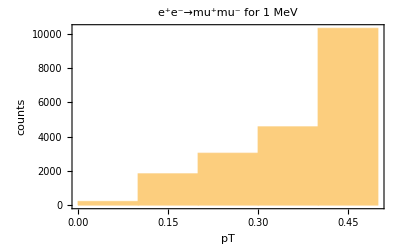

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 909.4_-4.36512^4.27418 | 0.00232286 | 1.45341
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 905.671_-4.36512^4.27418 | 0.00285421 | 1.60779
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 815.823_-4.0923^4.0923 | 0.0155279 | 3.55921
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 754.62_-3.91042^3.91042 | 0.0255638 | 4.39215
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 677.685_-3.72854^3.72854 | 0.039793 | 5.19299
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 581.198_-3.45572^3.45572 | 0.0535935 | 5.58108
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 469.523_-3.09196^3.09196 | 0.068531 | 5.67247
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 328.566_-2.63726^2.54632 | 0.083925 | 5.25118

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu1,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 1 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
(* Cut Tables *)
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr1,sigExpCutcounter1}=MCtoExpCutlist[sigcutcounter1,(σsig1mev*Lumipb)];
sigoverbkgd1=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter1[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter1]}];
significance1=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter1[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter1]}];
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr1,"N_sig^Exp"],Prepend[sigoverbkgd1,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance1,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

50 MeV

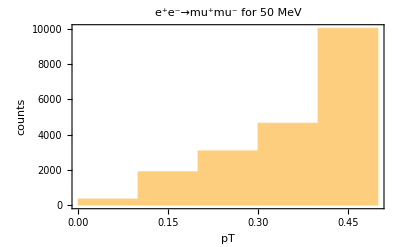

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu50,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 50 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr50,sigExpCutcounter50}=MCtoExpCutlist[sigcutcounter50,(σsig50mev*Lumipb)];
sigoverbkgd50=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter50[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter50]}];
significance50=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter50[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter50]}];
mev50=Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr50,"N_sig^Exp"],Prepend[sigoverbkgd50,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance50,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 916._-4.3968^4.3052 | 0.00233972 | 1.46396
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 905.649_-4.3052^4.3052 | 0.00285414 | 1.60775
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 813.042_-4.122^4.122 | 0.0154749 | 3.54708
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 752.402_-3.9388^3.9388 | 0.0254887 | 4.37924
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 671.978_-3.7556^3.7556 | 0.0394579 | 5.14925
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 578.912_-3.4808^3.4808 | 0.0533828 | 5.55913
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 459.099_-3.1144^3.1144 | 0.0670096 | 5.54653
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 314.371_-2.5648^2.5648 | 0.0802992 | 5.02432

```mathematica
Export["50MeV.pdf",mev50]
```

50MeV.pdf

150 MeV

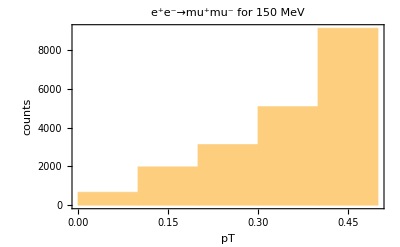

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu150,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 150 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr150,sigExpCutcounter150}=MCtoExpCutlist[sigcutcounter150,(σsig150mev*Lumipb)];
sigoverbkgd150=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter150[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter150]}];
significance150=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter150[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter150]}];
mev150=Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr150,"N_sig^Exp"],Prepend[sigoverbkgd150,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance150,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 925._-4.44^4.3475 | 0.00236271 | 1.47835
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 901.69_-4.3475^4.3475 | 0.00284166 | 1.60072
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 802.715_-4.07^4.07 | 0.0152784 | 3.50202
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 737.688_-3.9775^3.885 | 0.0249902 | 4.29359
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 657.952_-3.7^3.7 | 0.0386343 | 5.04178
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 553.52_-3.4225^3.4225 | 0.0510413 | 5.3153
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 422.633_-2.96^2.96 | 0.0616869 | 5.10597
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 249.38_-2.3125^2.3125 | 0.0636986 | 3.98562

```mathematica
Export["150MeV.pdf",mev150]
```

150MeV.pdf

200 MeV

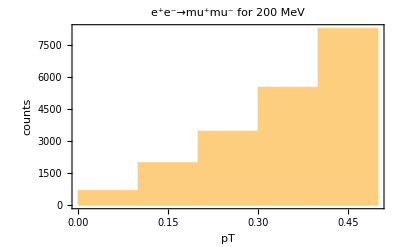

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu200,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 200 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr200,sigExpCutcounter200}=MCtoExpCutlist[sigcutcounter200,(σsig200mev*Lumipb)];
sigoverbkgd200=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter200[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter200]}];
significance200=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter200[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter200]}];
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr200,"N_sig^Exp"],Prepend[sigoverbkgd200,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance200,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 918.9_-4.41072^4.31883 | 0.00234713 | 1.4686
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 896.203_-4.31883^4.31883 | 0.00282437 | 1.59098
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 795.032_-4.04316^4.04316 | 0.0151321 | 3.46851
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 723.45_-3.85938^3.85938 | 0.0245079 | 4.21073
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 635.419_-3.6756^3.58371 | 0.0373112 | 4.86911
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 524.876_-3.30804^3.30804 | 0.0484 | 5.04023
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 381.16_-2.84859^2.7567 | 0.0556336 | 4.60492
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 136.365_-1.65402^1.65402 | 0.0348314 | 2.1794

250 MeV

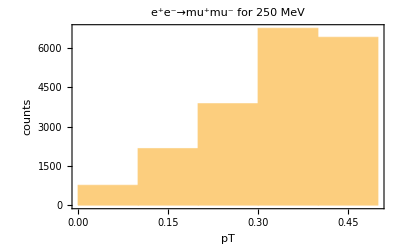

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu250,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 250 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr250,sigExpCutcounter250}=MCtoExpCutlist[sigcutcounter250,(σsig250mev*Lumipb)];
sigoverbkgd250=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter250[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter250]}];
significance250=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter250[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter250]}];
mev250=Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr250,"N_sig^Exp"],Prepend[sigoverbkgd250,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance250,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 904.8_-4.34304^4.25256 | 0.00231111 | 1.44606
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 884.894_-4.25256^4.25256 | 0.00278873 | 1.5709
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 772.337_-3.98112^3.98112 | 0.0147002 | 3.3695
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 695.158_-3.80016^3.80016 | 0.0235494 | 4.04606
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 596.625_-3.52872^3.43824 | 0.0350333 | 4.57184
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 467.148_-3.07632^3.07632 | 0.0430768 | 4.48589
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 290.531_-2.44296^2.44296 | 0.0424056 | 3.51001
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 0._0.^0. | 0. | 0.

```mathematica
Export["250mev.pdf",mev250]
```

250mev.pdf

300 MeV

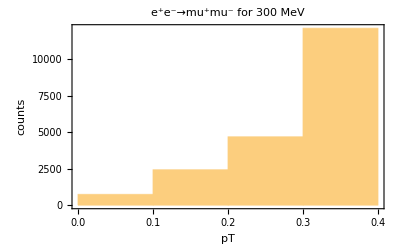

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu300,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 300 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr300,sigExpCutcounter300}=MCtoExpCutlist[sigcutcounter300,(σsig300mev*Lumipb)];
sigoverbkgd300=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter300[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter300]}];
significance300=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter300[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter300]}];
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr300,"N_sig^Exp"],Prepend[sigoverbkgd300,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance300,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 877.8_-4.21344^4.12566 | 0.00224215 | 1.40291
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 859.981_-4.12566^4.12566 | 0.00271022 | 1.52667
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 738.669_-3.86232^3.77454 | 0.0140594 | 3.22261
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 651.064_-3.59898^3.59898 | 0.0220557 | 3.78942
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 532.737_-3.24786^3.24786 | 0.0312818 | 4.08227
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 376.752_-2.72118^2.72118 | 0.0347411 | 3.61784
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 0._0.^0. | 0. | 0.
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 0._0.^0. | 0. | 0.

350 MeV

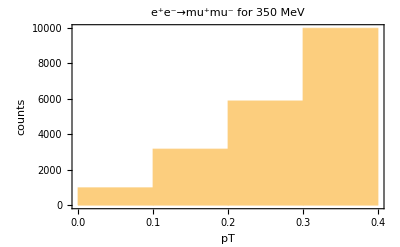

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu350,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 350 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr350,sigExpCutcounter350}=MCtoExpCutlist[sigcutcounter350,(σsig350mev*Lumipb)];
sigoverbkgd350=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter350[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter350]}];
significance350=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter350[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter350]}];
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr350,"N_sig^Exp"],Prepend[sigoverbkgd350,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance350,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 825.4_-3.96192^3.87938 | 0.0021083 | 1.31916
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 808.727_-3.87938^3.87938 | 0.00254869 | 1.43569
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 654.295_-3.46668^3.46668 | 0.0124534 | 2.85451
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 556.072_-3.21906^3.21906 | 0.0188377 | 3.23653
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 411.71_-2.80636^2.72382 | 0.0241752 | 3.15486
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 142.712_-1.6508^1.6508 | 0.0131598 | 1.37042
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 0._0.^0. | 0. | 0.
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 0._0.^0. | 0. | 0.

400 MeV

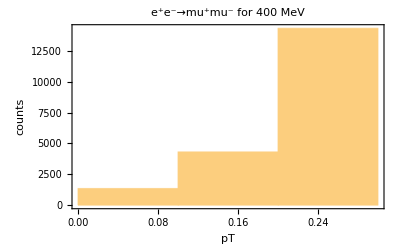

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu400,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 400 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr400,sigExpCutcounter400}=MCtoExpCutlist[sigcutcounter400,(σsig400mev*Lumipb)];
sigoverbkgd400=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter400[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter400]}];
significance400=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter400[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter400]}];
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr400,"N_sig^Exp"],Prepend[sigoverbkgd400,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance400,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 733.2_-3.51936^3.44604 | 0.0018728 | 1.17181
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 719.856_-3.44604^3.44604 | 0.00226861 | 1.27792
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 525.411_-2.9328^2.9328 | 0.0100003 | 2.29222
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 383.83_-2.5662^2.49288 | 0.0130028 | 2.23402
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 0._0.^0. | 0. | 0.
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 0._0.^0. | 0. | 0.
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 0._0.^0. | 0. | 0.
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 0._0.^0. | 0. | 0.

450 MeV

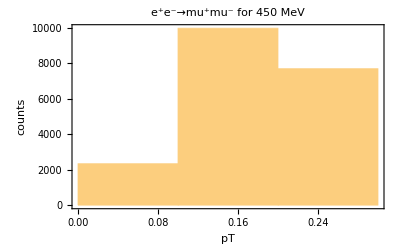

```mathematica
(* Now the Subscript[p, T] Histogram *)
Histogram[pTListu450,{0.1},PlotLabel->"e^+e^-→mu^+mu^- for 450 MeV", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgnd*Lumipb)];
{sigExpCutcounterErr450,sigExpCutcounter450}=MCtoExpCutlist[sigcutcounter450,(σsig450mev*Lumipb)];
sigoverbkgd450=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter450[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter450]}];
significance450=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter450[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter450]}];
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr450,"N_sig^Exp"],Prepend[sigoverbkgd450,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance450,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 391500._-1879.2^1840.05 | 566.6_-2.71968^2.66302 | 0.00144725 | 0.905546
Trigger: |η|<2.4 | 317311._-1683.45^1683.45 | 555.948_-2.66302^2.66302 | 0.00175206 | 0.986942
 p_T≥0.2 GeV | 52539.3_-704.7^665.55 | 217.914_-1.6998^1.64314 | 0.00414764 | 0.9507
 p_T≥0.25 GeV | 29519.1_-508.95^508.95 | 0._0.^0. | 0. | 0.
 p_T≥0.3 GeV | 17030.3_-391.5^391.5 | 0._0.^0. | 0. | 0.
 p_T≥0.35 GeV | 10844.6_-313.2^313.2 | 0._0.^0. | 0. | 0.
 p_T≥0.4 GeV | 6851.25_-234.9^234.9 | 0._0.^0. | 0. | 0.
 p_T≥0.45 GeV | 3915._-195.75^195.75 | 0._0.^0. | 0. | 0.

Question 11: Why do some of the cuts remove all the events for larger mass muons? (2 pts)
Answer: Because even in the range of the cut, none of the possibilities are probable.

## Putting together a summary plot

What is the take home message from this analysis? 
The most essential piece of information is what masses of new particle can be discovered. We do not know, before the experiment runs, what the mass of any new particle might be. So we must choose a strategy, in this case a particular p_T cut, and then describe the sensitivity of such a choice to the whole spectrum of masses.

Question 12: What p_T cut would you choose to make, and why? (4 pts)
Answer: I would choose to make a 0.35 p_T cut becuase it yields a 5 sigma for multiple muon masses.

Directive 17: Using your chosen cut (you must use the same cut for all masses) make a list of the form
{{muonmass, Nsig/√Nbkgnd},...}
for all the mass possibilities. Then make a plot of predicted sensitivity of this analysis. Make sure the regions of 5σ (discovery) and 2σ (exclusion) are marked. (5 pts)

```mathematica
plotData={{1,sigExpCutcounter1[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{50,sigExpCutcounter50[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{150,sigExpCutcounter150[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{200,sigExpCutcounter200[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{250,sigExpCutcounter250[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{300,sigExpCutcounter300[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{350,sigExpCutcounter350[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{400,sigExpCutcounter400[[6]]/Sqrt[bkgdExpCutcounter[[6]]]},{450,sigExpCutcounter450[[6]]/Sqrt[bkgdExpCutcounter[[6]]]}};
```

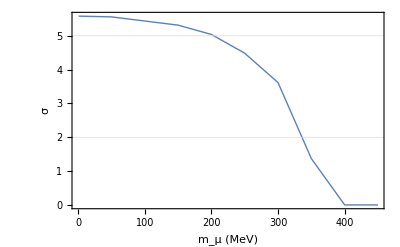

```mathematica
summaryFig=ListPlot[plotData,Joined->True,Frame->True,FrameLabel->{"m_μ (MeV)","σ"},BaseStyle->{FontSize->16},PlotStyle->Thick,FrameStyle->Thick,GridLines->{{},{5,2}},GridLinesStyle->{Thick,Dashed}]
```

Directive 18: Export the figure to pdf so that you can include it in your LATEX write-up. (5 pts)

```mathematica
Export["summaryFig.pdf",summaryFig]
```

summaryFig.pdf